```mathematica
((R^β)*x) / (( 1 + ( (R-1) / K)* x)^β)
```

R^β x (1+((-1+R) x)/K)^-β

```mathematica
D[(R^β x (1+((-1+R) x)/K)^-β), x]
```

R^β (1+((-1+R) x)/K)^-β-((-1+R) R^β x (1+((-1+R) x)/K)^(-1-β) β)/K

```mathematica
f[x_]:=R^β (1+((-1+R) x)/K)^-β-((-1+R) R^β x (1+((-1+R) x)/K)^(-1-β) β)/K
```

```mathematica
f[0]
```

R^β

```mathematica
f[K]
```

```mathematica
1-((-1+R) β)/R
1- β(1 - 1/R)
```

1-((-1+R) β)/R

```mathematica
Simplify[1-((-1+R) β)/R]
```

1+(-1+1/R) β

```mathematica
Simplify[1-(1-1/R) β]
```

1+(-1+1/R) β

```mathematica
.5^.01
```

0.993092

```mathematica
.5^.00001
```

0.999993

```mathematica
.01^10000
```

1.0000000000001×10^-20000

```mathematica
.01^.01
```

0.954993

```mathematica
.00001^.01
```

0.891251

```mathematica
1^.0000
```

1.

```mathematica
1^.000001
```

1.

```mathematica
1.2^.000001
```

1.

```mathematica
Reduce[{1-((-1+R) β)/R,R>0,β>0},R,Reals]
```

```mathematica
Reduce[{1-((-1+R) β)/R,R>0,β>0},R,Reals]
```

```mathematica
Reduce[{-1 <1-((-1+R) β)/R <1,R>0,β>0},R,Reals]
```

(0<β≤2&&R>1)||(β>2&&1<R<β/(-2+β))

```mathematica
(2x) / (x-1)
```

(2 x)/(-1+x)

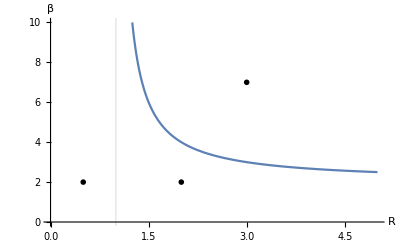

```mathematica
Plot[(2 x)/(-1+x),{x,0,5}, PlotRange->{{0, 5},{0,10}}, GridLines->{{1},{}},Epilog->
{Inset[Graphics[{Text["A"],Circle[]},ImageSize->30],{.5,+2}],Inset[Graphics[{Text["B"],Circle[]},ImageSize->30],{2,2}],
Inset[Graphics[{Text["C"],Circle[]},ImageSize->30],{3,7}]},AxesLabel->{R,β}]
```

```mathematica
f[x_,R_,β_]:=R^β (1+((-1+R) x)/K)^-β-((-1+R) R^β x (1+((-1+R) x)/K)^(-1-β) β)/K
```

```mathematica
f[K,1,1]
```

1

```mathematica
f[K,2,2]
```

0

```mathematica
f[K,3,3]
```

-1

```mathematica
f[K,4,3]
```

-5/4

```mathematica
5/4
```

5/4

```mathematica
N[5/4]
```

1.25

```mathematica
f[K,1,2]
```

1

```mathematica
f[K,1,3]
```

1

```mathematica
f[.5,4]
```

7.65404×10^-18

```mathematica
g[R_,β_]:=1-β(1- 1/R)
```

```mathematica
g[5,3]
```

-7/5

```mathematica
g[.5, 341]
```

342.

```mathematica
g[25,1]
```

1/25

```mathematica
g[1.01,10000000]
```

-99008.9

```mathematica
-r*x + K + K*r
```

```mathematica
2^.005
```

1.00347

```mathematica
2^.000000000005
```

1.

```mathematica
(I*x)^2
```

-x^2

```mathematica
(-I*x)^2
```

-x^2

```mathematica
Exp[-100*x^2]
```

ⅇ^(-100 x^2)

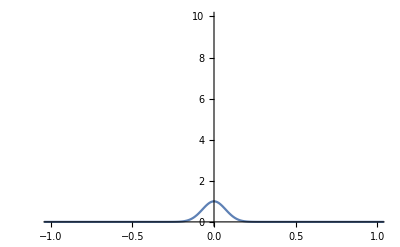

```mathematica
Plot[ⅇ^(-100 x^2),{x,-1.0392304845413263,1.0392304845413263}, PlotRange->{{-1, 1},{0, 10}}]
```

```mathematica
Exp[I*k*x]
```

ⅇ^(ⅈ k x)

```mathematica
ExpToTrig[ⅇ^(ⅈ k x)]
```

Cos[k x]+ⅈ Sin[k x]

```mathematica
11
```

```mathematica
1/I
```

-ⅈ

```mathematica
Exp[I*n*Pi*x/2]
```

ⅇ^(1/2 ⅈ n π x)

```mathematica
∫ⅇ^(1/2 ⅈ n π x)ⅆx
```

-(2 ⅈ ⅇ^(1/2 ⅈ n π x))/(n π)

```mathematica
f[x_,y_]:=x- y(x-1)
```

```mathematica
g[x_,y_]:=α*x*y - α*y-β*y
```

```mathematica
f[β/α +1, α/β + 1]
```

1+β/α-((1+α/β) β)/α

```mathematica
Simplify[1+β/α-((1+α/β) β)/α]
```

0

```mathematica
g[β/α +1, α/β + 1]
```

-α (1+α/β)-(1+α/β) β+α (1+α/β) (1+β/α)

```mathematica
Simplify[-α (1+α/β)-(1+α/β) β+α (1+α/β) (1+β/α)]
```

0

```mathematica
x/(x-1)
```

x/(-1+x)

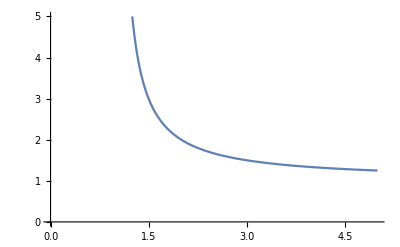

```mathematica
Plot[x/(-1+x),{x,0,5}, PlotRange->{{0, 5},{0,5}}]
```

```mathematica
Solve[x-y(x-1) ==0 , x]
```

{{x→y/(-1+y)}}

```mathematica
Solve[α*x*y - α*y - β*y == 0, x]
```

{{x→(α+β)/α}}

```mathematica
g[(α+β)/α, y]
```

-y α-y β+y (α+β)

```mathematica
Simplify[-y α-y β+y (α+β)]
```

0

```mathematica
((α + β) / α) / ((α + β) / α - 1)
```

(α+β)/(α (-1+(α+β)/α))

```mathematica
Simplify[(α+β)/(α (-1+(α+β)/α))]
```

(α+β)/β

```mathematica
Solve[(x/y)^2 - 4x - 4y ==0, x]
```

```mathematica
(α / β)^2 - 4(α+β)
```

α^2/β^2-4 (α+β)

```mathematica
Together[α^2/β^2-4 (α+β)]
```

(α^2-4 α β^2-4 β^3)/β^2

```mathematica
xy (1/y - 1 + 1/x)
```

```mathematica
Simplify[x*y (-1+1/x+1/y)]
```

x+y-x y

```mathematica
(x - y*(x-1)) / (x*y)
```

(x-(-1+x) y)/(x y)

```mathematica
Simplify[(x-(-1+x) y)/(x y)]
```

-1+1/x+1/y

```mathematica
D[(-1+1/x+1/y), x]
```

-1/x^2

```mathematica
(α*x*y - α*y - β*y) / (x*y)
```

(-y α+x y α-y β)/(x y)

```mathematica
Simplify[(-y α+x y α-y β)/(x y)]
```

```mathematica
D[-(α-x α+β)/x, y]
```

0

```mathematica
9/4
```

9/4

```mathematica
N[9/4]
```

2.25

```mathematica
4.5/4
```

1.125

```mathematica
Solve[α^2/β^2-4 (α+β) ==0, α]
```

{{α→2 (β^2-β^(3/2) √(1+β))},{α→2 (β^2+β^(3/2) √(1+β))}}

```mathematica
zp[a_, b_]:= -a/b + Sqrt[ (a/b)^2 - 4*(a+b)]/2
```

```mathematica
zm[a_, b_]:= -a/b -  Sqrt[ (a/b)^2 - 4*(a+b)]/2
```

```mathematica
zp[6, 1.5]
```

-4.+1.87083 ⅈ

```mathematica
zm[6, 1.5]
```

-4.-1.87083 ⅈ

```mathematica
zp[4,2]
```

-2+ⅈ √5

```mathematica
zp[4,1]
```

-4+ⅈ

```mathematica
zp[5,1]
```

-9/2

```mathematica
zm[5,1]
```

-11/2

```mathematica
2*(1  -  Sqrt[2])
```

2 (1-√2)

```mathematica
N[2 (1-√2)]
```

-0.828427

```mathematica
N[2 (1+√2)]
```

4.82843

```mathematica
Sin[l*Pi*z/L]
```

Sin[(l π z)/L]

```mathematica
D[Sin[(l π z)/L],{z,2}] / Sin[(l π z)/L]
```

-(l^2 π^2)/L^2

```mathematica
300*Sqrt[((2.40483^2) / .00001 + (Pi^2) / (.5^2))]
```

228150.

```mathematica
Pn[n_]:= Simplify[(1 / ( (2^n)* (n!)) ) * Evaluate[D[ (x^2-1)^n, {x, n}]]]
```

```mathematica
Pn[2]
```

1/2 (-1+3 x^2)

```mathematica
An[n_] := Simplify[ ((2*n + 1)/ 2) * Evaluate[Integrate[Evaluate[x * Pn[n]], {x,0,1}]]]
```

```mathematica
An[2]
```

5/16

```mathematica
An[1]
```

1/2

```mathematica
96/48
```

2

```mathematica
Pn[3]
```

1/2 x (-3+5 x^2)

```mathematica
120/48
```

5/2

```mathematica
72/48
```

3/2

```mathematica
35/20 - 21/12
```

0

```mathematica
An[3]
```

0

```mathematica
An[4]
```

-3/32

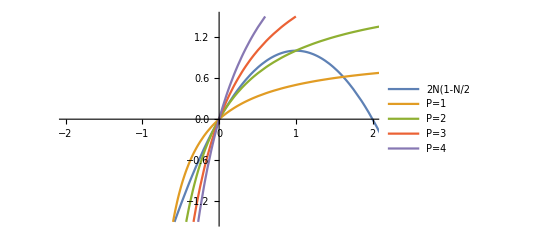

```mathematica
Plot[{2*x*(1-x/2), x/(1+x), 2x/(1+x), 3x/(1+x), 4x/(1+x)}, {x, -10,10},PlotRange->{{-2,2},{-1.5,1.5}},PlotLegends->{"2N(1-N/2", "P=1", "P=2", "P=3", "P=4"}]
```

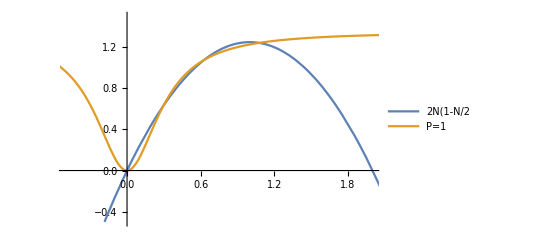

```mathematica
Plot[{2.5*x*(1-x/2), 1.35*x^2/(.1+x^2)}, {x, -10,10},PlotRange->{{-.5,2},{-.5,1.5}},PlotLegends->{"2N(1-N/2", "P=1"}]
```

```mathematica
16*4*3*2
```

384

```mathematica
16*3
```

48

```mathematica
96*2
```

192

```mathematica
192*2
```

384

```mathematica
5*192
```

960

```mathematica
3*192
```

576

```mathematica
48+96
```

144

```mathematica
192+384+960
```

1536

```mathematica
-192-384-576
```

-1152

```mathematica
144/384
```

3/8

```mathematica
1536/384
```

4

```mathematica
1152/384
```

3

```mathematica
Clear[x]
```

```mathematica
Pn[4]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
D[(x^2-1)^4, x]
```

8 x (-1+x^2)^3

```mathematica
D[(8 x (-1+x^2)^3), x]
```

48 x^2 (-1+x^2)^2+8 (-1+x^2)^3

```mathematica
D[(48 x^2 (-1+x^2)^2+8 (-1+x^2)^3), x]
```

192 x^3 (-1+x^2)+144 x (-1+x^2)^2

```mathematica
D[(192 x^3 (-1+x^2)+144 x (-1+x^2)^2), x]
```

384 x^4+1152 x^2 (-1+x^2)+144 (-1+x^2)^2

```mathematica
D[(384 x^4+1152 x^2 (-1+x^2)+144 (-1+x^2)^2), x]
```

3840 x^3+2880 x (-1+x^2)

```mathematica
288*2
```

576

```mathematica
6144+576
```

6720

```mathematica
-2304-576
```

-2880

```mathematica
144*4
```

576

```mathematica
5*192
```

960

```mathematica
3*192
```

576

```mathematica
576+960
```

1536

```mathematica
576*2
```

1152

```mathematica
4*144
```

576

```mathematica
1536*4
```

6144

```mathematica
1152*2
```

2304

```mathematica
6720/384
```

35/2

```mathematica
2880/384
```

15/2

```mathematica
(3840 x^3+2880 x (-1+x^2))/384
```

1/384 (3840 x^3+2880 x (-1+x^2))

```mathematica
Simplify[1/384 (3840 x^3+2880 x (-1+x^2))]
```

5/2 x (-3+7 x^2)

```mathematica
(9/2)*(35/2)
```

315/4

```mathematica
9*15
```

135

```mathematica
(315/4)*(1/5) - (135/4)*(1/3)
```

9/2

```mathematica
An[4]
```

-3/32

```mathematica
9*35
```

```mathematica
Pn[4]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
(x^2-1)^4
```

(-1+x^2)^4

```mathematica
D[(-1+x^2)^4, x]
```

8 x (-1+x^2)^3

```mathematica
D[(8 x (-1+x^2)^3), x]
```

48 x^2 (-1+x^2)^2+8 (-1+x^2)^3

```mathematica
D[(48 x^2 (-1+x^2)^2+8 (-1+x^2)^3), x]
```

192 x^3 (-1+x^2)+144 x (-1+x^2)^2

```mathematica
D[(192 x^3 (-1+x^2)+144 x (-1+x^2)^2), x]
```

384 x^4+1152 x^2 (-1+x^2)+144 (-1+x^2)^2

```mathematica
Expand[384 x^4+1152 x^2 (-1+x^2)+144 (-1+x^2)^2]
```

144-1440 x^2+1680 x^4

```mathematica
1680/384
```

35/8

```mathematica
1440/384
```

15/4

```mathematica
1440/384
```

15/4

```mathematica
Pn[4]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
Expand[1/8 (3-30 x^2+35 x^4)]
```

3/8-(15 x^2)/4+(35 x^4)/8

```mathematica
(9/2)*(35/8)
```

315/16

```mathematica
(9/2)*(15/4)
```

135/8

```mathematica
(9/2)*(3/8)
```

27/16

```mathematica
(315/16)*(1/6) - (135/8)*(1/4) + (27/16)*(1/2)
```

-3/32

```mathematica
An[4]
```

-3/32

```mathematica
Pn[4]*x
```

1/8 x (3-30 x^2+35 x^4)

```mathematica
∫_0^1 1/8 x (3-30 x^2+35 x^4)ⅆx
```

```mathematica
-1/48*(9/2)
```

-3/32

```mathematica
Pn[4]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
Expand[1/8 (3-30 x^2+35 x^4)]
```

3/8-(15 x^2)/4+(35 x^4)/8

```mathematica
An[4]
```

-3/32

```mathematica
An[3]
```

0

```mathematica
An[2]
```

5/16

```mathematica
Pn[2]
```

1/2 (-1+3 x^2)

```mathematica
Expand[1/2 (-1+3 x^2)]
```

-1/2+(3 x^2)/2

```mathematica
An[1]
```

1/2

```mathematica
Pn[1]
```

x

```mathematica
An[4]
```

-3/32

```mathematica
a0=1/4
p0=1
a1=1/2
p1=x
a2=5/16
p2 = (3/2)*x^2 - 1/2
a3=0
p3=(5/2)*x^3 - (3/2)*x
a4=-3/32
p4 = (35/8)*x^4 - (15/4)*x^2 + 3/8
```

1/4

1

1/2

x

5/16

-1/2+(3 x^2)/2

0

-(3 x)/2+(5 x^3)/2

-3/32

3/8-(15 x^2)/4+(35 x^4)/8

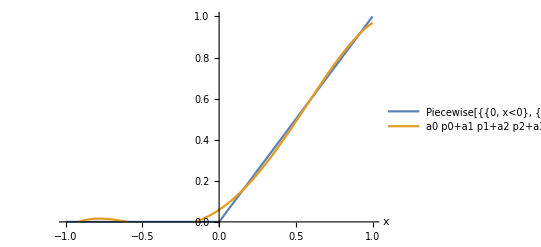

```mathematica
Plot[{Piecewise[{{0, x <0},{x, x>0}}], a0*p0+a1*p1+a2*p2+a3*p3+a4*p4}, {x,-1,1}, PlotRange->{{-1,1},{0,1}}, AxesLabel->Automatic, PlotLegends->"Expressions"]
```

```mathematica
An[3]
```

0

```mathematica
35/20 - 21/12
```

0

```mathematica
Solve[r-r*N/k - c*P/(a+N) == 0, P]
```

{{P→-((a+N) (-k+N) r)/(c k)}}

```mathematica
Expand[-((a+N) (-k+N) r)/(c k)]
```

(a r)/c+(N r)/c-(a N r)/(c k)-(N^2 r)/(c k)

```mathematica
-x^2+x + 1
```

1+x-x^2

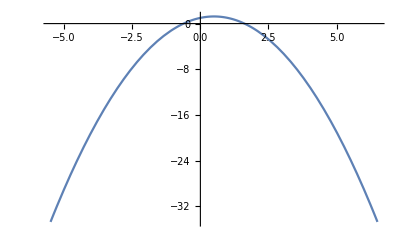

```mathematica
Plot[1+x-x^2,{x,-5.5,6.5}]
```

```mathematica
Solve[r*N*(1-N/k) - c*N*P/(a+N) == 0, P ]
```

{{P→-((a+N) (-k+N) r)/(c k)}}

```mathematica
Solve[r*N(1-N/k) - (P*c*N^2)/(a^2 + N^2)==0, P]
```

{{P→((k-N) (a^2+N^2) r)/(c k N)}}

```mathematica
Expand[((k-N) (a^2+N^2) r)/(c k N)]
```

-(a^2 r)/(c k)+(a^2 r)/(c N)+(N r)/c-(N^2 r)/(c k)

```mathematica
-x^2 + x + 1/x -1
```

-1+1/x+x-x^2

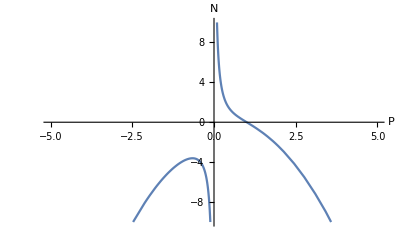

```mathematica
Plot[-1+1/x+x-x^2,{x,-8,8}, PlotRange->{{-5, 5}, {-10 , 10}}, AxesLabel->{"P", "N"}]
```

```mathematica
s
```

```mathematica
r*N(1-N/k) - (P*c*N^2)/(a^2 + N^2)
```

-(c N^2 P)/(a^2+N^2)+N (1-N/k) r

```mathematica
D[-(c N^2 P)/(a^2+N^2)+N (1-N/k) r, N]
```

(2 c N^3 P)/((a^2+N^2)^2)-(2 c N P)/(a^2+N^2)-(N r)/k+(1-N/k) r

```mathematica
F[N_]:=(2 c N^3 P)/((a^2+N^2)^2)-(2 c N P)/(a^2+N^2)-(N r)/k+(1-N/k) r
```

```mathematica
F[0]
```

r

```mathematica
Solve[r*N(1-N/k) - (P*c*N^2)/(a^2 + N^2)==0, P]
```

{{P→((k-N) (a^2+N^2) r)/(c k N)}}

```mathematica
Simplify[1/Sqrt[10]]
```

1/(√10)

```mathematica
D[r*N(1 - N/K) - (c*N*P) / (a + N), N]
```

(c N P)/(a+N)^2-(c P)/(a+N)-(N r)/K+(1-N/K) r

```mathematica
b[N_]:=(c N P)/(a+N)^2-(c P)/(a+N)-(N r)/K+(1-N/K) r
```

```mathematica
b[0]
```

-(c P)/a+r